This notebook calculates the accumulated charge (probability density) around a singular magnetic flux tube (blue square)

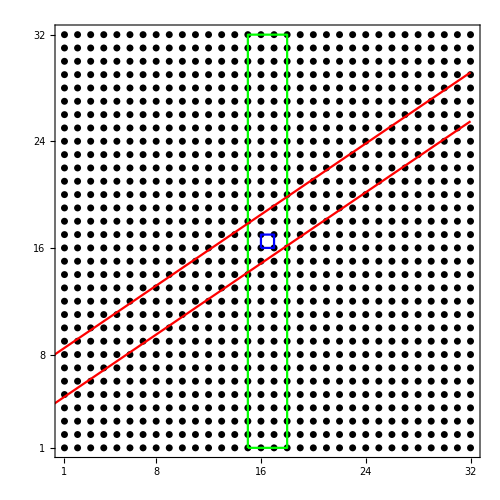

We take a Weyl SemiMetal, implemented on real space along x and y directions, and k_z is taken as a good quantum number.

The Magnetic Field is introduced using Peierls substitution in the hopping amplitudes

Then we project the parent crystal to the Brane between the red lines

We keep changing the magnetic field, and study how the accumulated charge changes (between the green lines) with increasing magnetic field, and average it over kz values uniformly taken between -π and π

The data is gathered and plotted in ChiralAnomaly_Projected_data.nb

We take electric charge e and reduced Planck’s constant ℏ to be unity.

```mathematica
(*---------------------------------------------------------------------------------------------*)
```

```mathematica
tStart = AbsoluteTime[];
```

```mathematica
Clear[Lx,Ly,PtsInKzSpace,A,B,
sx2d,SX2D,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
(** Change system size here **)
```

```mathematica
Lx=32;
Ly=32;
midPtX = Floor[Lx/2];
midPtY = Floor[Ly/2];
A=Lx*Ly;
PtsInKzSpace=20;
```

```mathematica
(** The magnetic field is defined in units of 2π **)
```

```mathematica
B=0.06*2*π;
```

```mathematica
(**--------------Define hopping matrices in the parent lattice-----------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2 Exp[- I B],sy2d[(k+1)Lx+j,k Lx+j]=I/2 Exp[ I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]
Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2 Exp[- I B],cy2d[(k+1)Lx+j,k Lx+j]=1/2 Exp[I B]},{j,midPtX+1,Lx}],{k,midPtY,midPtY}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(** Define the Hamiltonian **)
```

```mathematica
(** PBC along y is αy = 1, OBC along is αy = 0 **)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_, αy_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-2t0*(CX2D+CY2D+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*-----------------------Create a vector containing the kz values--------------------------------------*)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,PtsInKzSpace-1]
```

{-3.14159,-2.8109,-2.4802,-2.14951,-1.81882,-1.48812,-1.15743,-0.826735,-0.496041,-0.165347,0.165347,0.496041,0.826735,1.15743,1.48812,1.81882,2.14951,2.4802,2.8109,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

20

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[SitesWithMagFieldInside,Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
SitesWithMagFieldInside = {{midPtX,midPtY},{midPtX+1,midPtY},{midPtX+1,midPtY+1},{midPtX,midPtY+1},{midPtX,midPtY}};
```

```mathematica
SitesSummedOver ={{midPtX-1,1},{midPtX+2,1},{midPtX+2,Ly},{midPtX-1,Ly},{midPtX-1,1}};
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
(**  LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8.5
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+5.5 **)
```

```mathematica
(**-------Rational-------**)
```

```mathematica
LineUp[x_]:=(2/3)(x-1)+8.5
LineDn[x_]:=(2/3)*(x-2)+5.5
```

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[SitesWithMagFieldInside,PlotStyle-> {Blue,PointSize[0.01]},Joined-> True],
ListPlot[SitesSummedOver,PlotStyle-> {Green,PointSize[0.01]},Joined-> True],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{8,"8"},{16,"16"},{24,"24"},{32,"32"}},None},{{{1,"1"},{8,"8"},{16,"16"},{24,"24"},{32,"32"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

-Graphics-

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to isolate points inside the projected brane (between the red lines), store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew];
```

```mathematica
(** List of Y coordinates of the sites in the projected brane **)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
(** List of X coordinates of the sites in the projected brane **)
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(** Repeat the coordinates for the two onsite orbitals **)
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
(** This list contains (original) indices of the orbitals within the projected brane **)
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsBrane=Dimensions[TotalFibon][[1]]
```

236

```mathematica
NOrbitalsBrane/2
```

118

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsBrane
```

1812

```mathematica
PercentageDataIn = N[NOrbitalsBrane/(2*A)]
```

0.115234

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2048}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(** Calculate Charge density as a function of position **)
```

```mathematica
Clear[ChargeXY, ChargeXYFlatten, ChargeXYPlot]
```

```mathematica
ChargeXY = Table[{x,y,0},{x,1,Lx},{y,1,Ly}];
```

```mathematica
Dimensions[ChargeXY]
```

{32,32,3}

```mathematica
(** Here we calculate the total charge (probability density) at each point on the projected lattice for each value of kz, and add them **)
```

```mathematica
Do[{Clear[HTrial,ValueFibon,VecFibon,ValVecFibon,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial =HamiltonianWSM1[1,0.5,0,1,kzVector[[kzIndex]],1],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsBrane}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsBrane}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsBrane}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor],
ValVecFibon=SortBy[Transpose[{Re[ValueFibon],VecFibon}],First],
Do[Do[{Clear[x,y],x=XList[[n]],y=YList[[n]],ChargeXY[[x,y]][[3]] += Abs[ValVecFibon[[J,2,2n]]]^2+Abs[ValVecFibon[[J,2,2n-1]]]^2},{n,1,NOrbitalsBrane/2}],{J,1,NOrbitalsBrane/2}]},{kzIndex ,1,PtsInKzSpace}];
```

```mathematica
(** This contains data for (x,y,ChargeAtPoint(x,y)))
```

```mathematica
ChargeXY;
```

```mathematica
ChargeXYFlatten = Flatten[ChargeXY];
```

```mathematica
Dimensions[ChargeXYFlatten][[1]]
```

3072

```mathematica
Lx*Ly*3
```

3072

```mathematica
(** Here we sum all the charges on the sites within the projected brane, between the green line **)
```

```mathematica
(** to measure in the unit of e/π, we multiply with π **)
```

```mathematica
deltaQ = π * Sum[(ChargeXY[[x,y]][[3]])/PtsInKzSpace,{x,midPtX-1,midPtX+2},{y,1,Ly}]
```

44.0763

```mathematica
B
```

0.376991

```mathematica
phiOverPhi0 = N[B/(2*π)]
```

0.06

```mathematica
(** We collect the value of deltaQ and phiOverPhi0 for different values of magnetic field B. Then we store them and plot them in  ChiralAnomaly_Projected_data.nb **)
```

```mathematica
tStop = AbsoluteTime[];
timeTakenInSeconds = tStop - tStart
```